```mathematica
c=1;
u2=-c/2 Csch[(√c)/2(x-c t)]^2;
v2=-c/2 Csch[(√c)/2(ξ)]^2;
Simplify[D[u2,t]+6u2 D[u2,x]+D[u2,{x,3}]]
```

0

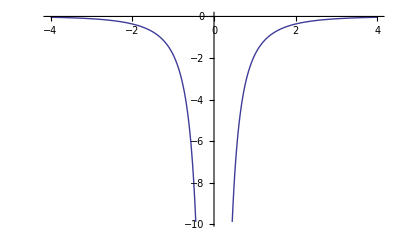

-Graphics3D-

```mathematica
c=1;
u2=-c/2 Csch[(√c)/2(x-c t)]^2;
v2=-c/2 Csch[(√c)/2(ξ)]^2;
Plot[v2,{ξ,-4,4}]
Plot3D[u2,{x,-6,6},{t,-2,2}]
```

0

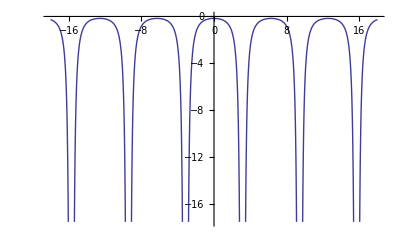

-Graphics3D-

```mathematica
c=1;
u5=-c/6-c/2 Tan[(√c)/2(x-c t)]^2;
v5=-c/6-c/2 Tan[(√c)/2(ξ)]^2;
Simplify[D[u5,t]+6u5 D[u5,x]+D[u5,{x,3}]]
Plot[v5,{ξ,-18,18}]
Plot3D[u5,{x,-6,6},{t,-2,2}]
```